```mathematica
timesDFS=Import[NotebookDirectory[]<>"tests/random-1000-15000/times-DFS.txt","Table"]//Flatten
timesBFS=Import[NotebookDirectory[]<>"tests/random-1000-15000/times-BFS.txt","Table"]//Flatten
timesRandom=Import[NotebookDirectory[]<>"tests/random-1000-15000/times-random.txt","Table"]//Flatten
sizes=Import[NotebookDirectory[]<>"tests/random-1000-15000/sizes.txt","Table"]//Flatten
```

{0.08075,0.1612,0.2275,0.3033,0.3797,0.4537,0.5286,0.6112,1.799,2.103,2.309,2.535,2.682,2.844,4.829,0.3275,0.2667,0.1083,0.1109,0.11}

{0.06726,0.3472,0.499,0.6614,0.8396,0.9654,1.159,1.289,1.475,1.634,1.734,1.859,1.876,1.876,2.926,0.2698,0.1999,0.1472,0.1018,0.1011}

{0.09313,0.173,0.254,0.3392,0.4282,0.5174,0.5991,0.6898,0.787,2.318,2.521,2.722,2.88,2.806,4.21,0.2087,0.1603,0.0955,0.09228,0.08972}

{999,1998,2997,3996,4995,5994,6993,7992,8991,9990,10989,11988,12987,13986,14985,15000,15000,15000,15000,15000}

```mathematica
ks=Table[i,{i,Length[timesDFS]}];
```

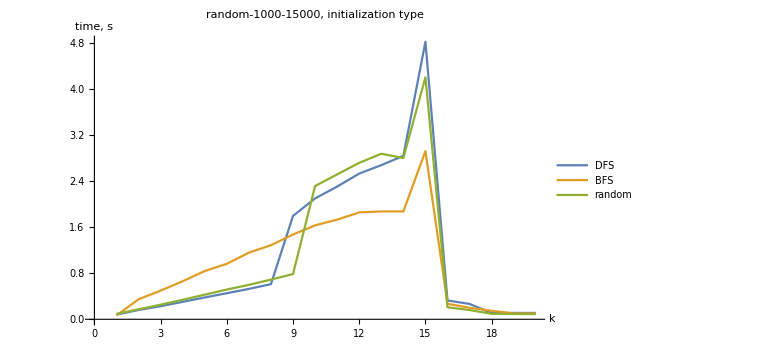

```mathematica
ListLinePlot[
{{ks,timesDFS}//Transpose,{ks,timesBFS}//Transpose,{ks,timesRandom}//Transpose},
ImageSize->Large,AxesLabel->{"k","time, s"},
PlotLabel->"random-1000-15000, initialization type",LabelStyle->Directive[14],
PlotLegends->{"DFS","BFS","random"}]
```

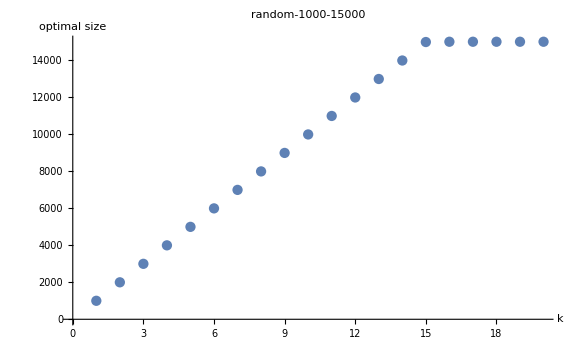

```mathematica
ListPlot[
{ks,sizes}//Transpose,
ImageSize->Large,AxesLabel->{"k","optimal size"},PlotLabel->"random-1000-15000",LabelStyle->Directive[14]]
```

```mathematica
timesDFS=Import[NotebookDirectory[]<>"tests/delaunay/times-DFS.txt","Table"]//Flatten
timesBFS=Import[NotebookDirectory[]<>"tests/delaunay/times-BFS.txt","Table"]//Flatten
timesRandom=Import[NotebookDirectory[]<>"tests/delaunay/times-random.txt","Table"]//Flatten
```

{0.7938,1.606,9.79,0.5977,0.6094,0.6195,0.6295,0.6374,0.6503,0.6587}

{0.7988,3.71,38.22,0.8238,0.5882,0.6124,0.6439,0.6693,0.6953,0.727}

{0.813,3.824,12.43,0.6281,0.359,0.3317,0.3188,0.3139,0.3122,0.313}

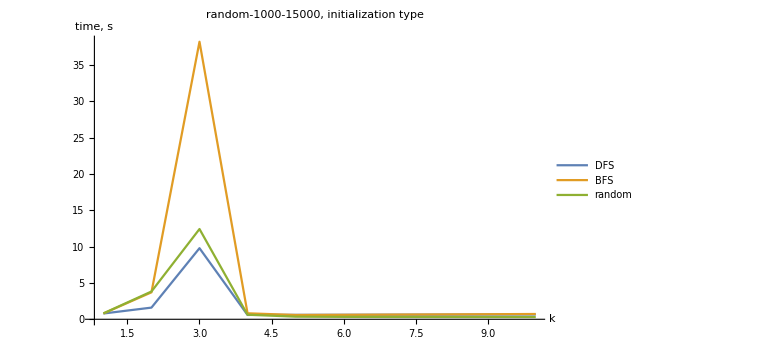

```mathematica
ListLinePlot[
{timesDFS,timesBFS,timesRandom},
ImageSize->Large,AxesLabel->{"k","time, s"},
PlotLabel->"random-1000-15000, initialization type",LabelStyle->Directive[14],
PlotLegends->{"DFS","BFS","random"},PlotRange->All]
```